# ランチェスターの法則（1次法則）

## プログラム前の注意点

```mathematica
以下ではローカルに変数を代入するためにModule[]を使う
```

```mathematica
a=.;b=.
```

```mathematica
Module[{a=3,b=5},a+b]
a+b
```

## よく使う内蔵関数 ( 詳細はセルを展開して確認 )

#### If文について

```mathematica
If[condition,t,f]
condition の評価の結果がTrueとなる場合に t を，Falseとなる場合に f を返す．
```

```mathematica
a=3;
If[a>1,1000,-1000]
```

```mathematica
If[a>5,1000,-1000]
```

```mathematica
If[]をTableに入れることもできる．
```

```mathematica
x={1,2,3,4,5,6};
Table[If[x⟦i⟧>3,1000,-1000],{i,1,5}]
```

```mathematica
問題：おみくじを作ってみよう
1.乱数を発生させる
2.乱数が0～0.2の間の数なら大吉，
0.2～0.4の間なら中吉，
などのルールをIf文で書く
3.　関数omikujiを定義する
4.　今日の運勢は？
```

#### Appendの使い方

```mathematica
Append[{a,b,c,d},x]
```

```mathematica
x={};
Append[x,1]
```

```mathematica
(* Appendを反復的に繰り返す *)
x={};
Do[x=Append[x,i],{i,1,10}];
x
```

#### RandomSampleの使い方

```mathematica
RandomSample[{1,2,3,4,5}]
```

#### Do 繰り返し (Forを簡略化したもの)

```mathematica
{{, Do[expr,{Subscript[i, max]}]
式expr をSubscript[i, max] 回評価する．}}
{{, Do[expr,{i,Subscript[i, max]}]
変数 i の値が1から Subscript[i, max] まで刻み幅1で式 expr を順に評価する．}}
```

```mathematica
(*　最初にx=5を代入して，次にxにx+1を再帰的に代入する．これを10回繰り返す　*)
x=5;
Do[x=x+1,{10}];
x
```

15

```mathematica
(* Doそのものはvoid関数である．よってデフォルトの出力はない *)
x=5;
Do[x=x+1,{10}]
```

#### While（条件を満たす限り繰り返す）

```mathematica
n<4という条件を満足させながら，n を出力し1つずつ増加させる
```

```mathematica
n=1;While[n<4,Print[n];n++]
```

1

2

3

## ワンショット

```mathematica
グループ1とグループ2の戦士が招集される．
初期条件
・各兵士の武力は正規分布にしたがう．
・兵士達は敵国の兵士と，騎士道精神に則り一対一で戦う．(対戦はランダム)

x,yを兵数として，戦闘能力をそれぞれa,bとおけば，微分方程式は
dx/dt==-b,dy/dt==-a
である
```

### 1回の戦闘結果を出力するModule

```mathematica
Module[{id1,id2,n1=20,n2=20,power1,power2,winner1,winner2},
id1=Range[n1];(*初期兵ID*)
id2=Range[n2];(*初期兵ID*)

(*　集団別に兵力を　*)
power1=Table[RandomReal[NormalDistribution[50,1]],{n1}];
power2=Table[RandomReal[NormalDistribution[51,1]],{n2}];

(* 戦闘力を比較して勝者を残す*)
winner1={};
winner2={};

Table[
If[
power1⟦id1⟦i⟧⟧>power2⟦id2⟦i⟧⟧,
winner1=Append[winner1,id1⟦i⟧],
winner2=Append[winner2,id2⟦i⟧]
](* If *),
{i,1,Min[n1,n2]}](* Table *);

Print[{グループ1戦闘後,winner1}];
Print[{グループ2戦闘後,winner2}];
Print[{"戦闘力の組み合わせ",MatrixForm[Table[{i,N[power1⟦i⟧,3],N[power2⟦i⟧,3]},{i,1,Min[n1,n2]}]]}]
]
```

{ー グル プ1戦闘後,{}}

{ー グル プ2戦闘後,{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}}

{戦闘力の組み合わせ,(1 | 49.5321 | 50.229
2 | 49.9137 | 51.2748
3 | 51.1351 | 53.7604
4 | 49.1489 | 50.872
5 | 50.4876 | 51.3145
6 | 50.2007 | 52.7917
7 | 48.9579 | 50.4654
8 | 49.3318 | 50.6185
9 | 49.2707 | 51.3208
10 | 49.9689 | 51.2805
11 | 49.9008 | 51.0453
12 | 48.0213 | 51.1775
13 | 50.5272 | 50.6905
14 | 47.9872 | 50.3475
15 | 49.9049 | 51.8186
16 | 51.1981 | 51.3673
17 | 49.9932 | 51.6758
18 | 50.6235 | 52.1548
19 | 49.6602 | 50.8396
20 | 50.475 | 51.9917)}

### For文 を使った別の表現

```mathematica
Module[{army1,army2,winner1={},winner2={},list1={}},
For[i=1,i<=20,i++,
army1=RandomReal[NormalDistribution[50,1]];
army2=RandomReal[NormalDistribution[52,2]];
list1=Append[list1,{i,army1,army2}];
If[army1>army2,winner1=Append[winner1,army1],
winner2=Append[winner2,army2]]
](* For終了 *);
Print[{"army1戦闘後 ",winner1}];
Print[{"army2戦闘後 ",winner2}];
Print[{"戦闘力の組み合わせ",MatrixForm[list1]}]
]
```

{army1戦闘後 ,{50.8195,50.3897,50.5872,52.1061,50.5497}}

{army2戦闘後 ,{51.1943,53.0208,53.2124,54.8082,53.1402,53.0769,52.815,50.7171,54.0717,54.1638,52.0057,51.6935,51.1285,53.9148,53.5629}}

{戦闘力の組み合わせ,(1 | 50.4908 | 51.1943
2 | 50.8195 | 50.2314
3 | 50.0469 | 53.0208
4 | 48.7681 | 53.2124
5 | 50.4463 | 54.8082
6 | 50.3897 | 49.1821
7 | 49.0055 | 53.1402
8 | 50.5872 | 48.4907
9 | 48.6918 | 53.0769
10 | 50.0874 | 52.815
11 | 50.1132 | 50.7171
12 | 52.1061 | 49.5358
13 | 50.5497 | 48.5332
14 | 51.3327 | 54.0717
15 | 49.4323 | 54.1638
16 | 51.3104 | 52.0057
17 | 49.6114 | 51.6935
18 | 50.7446 | 51.1285
19 | 50.7149 | 53.9148
20 | 50.7329 | 53.5629)}

```mathematica
問題
より興味深いシミュレーションにするためには,どのようなシナリオを追加すればよいか?
```

## 各クロージャの説明

### 国1と国2の戦士が同数招集される．初期条件として各兵士の武力は正規分布にしたがう．

```mathematica
Module[{id1,id2,power1,power2,n=10},
id1=Range[n];id2=Range[n];(*　兵士の番号を出力　*)
power1=Table[RandomReal[NormalDistribution[10,1]],{n}];(*　1国兵士の武力を定義する　*)
power2=Table[RandomReal[NormalDistribution[12,1]],{n}];(*　2国兵士の武力を定義する　*)
Print[{power1,power2}];
id1=RandomSample[id1];
id2=RandomSample[id2];(*　ランダムに並び替える　*)
Print[{id1,id2}];
power1=Table[power1⟦id1⟦i⟧⟧,{i,1,n}];
power2=Table[power2⟦id1⟦i⟧⟧,{i,1,n}];
Print[{power1,power2}](* id1,id2の番号で呼び出した兵士の兵力 *)
]
```

{{10.3669,10.7537,10.9809,11.1658,9.67576,9.28828,9.21689,9.9837,8.99814,8.94759},{12.222,11.3155,11.1179,13.2001,11.942,13.4868,12.2957,12.5764,10.3736,12.0089}}

{{9,10,4,5,7,3,8,6,1,2},{3,5,1,6,2,9,7,8,4,10}}

{{8.99814,8.94759,11.1658,9.67576,9.21689,10.9809,9.9837,9.28828,10.3669,10.7537},{10.3736,12.0089,13.2001,11.942,12.2957,11.1179,12.5764,13.4868,12.222,11.3155}}

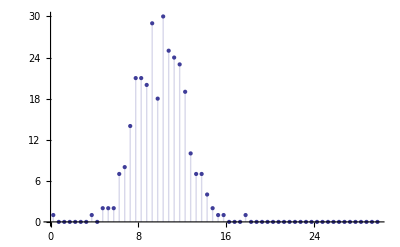

```mathematica
(* 兵力分布をグラフで確認してみる　*)
Module[{dist,bin,memori},
dist=Table[RandomReal[NormalDistribution[10,2]],{300}];
bin=BinCounts[dist,{0,30,0.5}];
(* 0.5の幅に何人いるかをカウント．distをそのままプロットしても意味無し *)
memori=Table[i,{i,0.25,30,0.5}];(* 目盛りを定義 *)
ListPlot[Transpose[{memori,bin}],Filling->Axis]
]
```

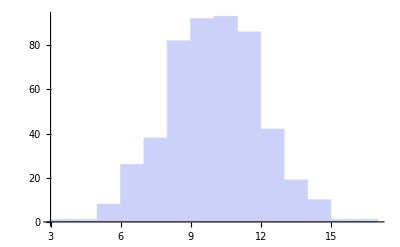

```mathematica
(* 兵力分布をグラフで確認してみる　ver10　　Histogram　使用　*)
Histogram[Table[RandomReal[NormalDistribution[10,2]],{500}]]
```

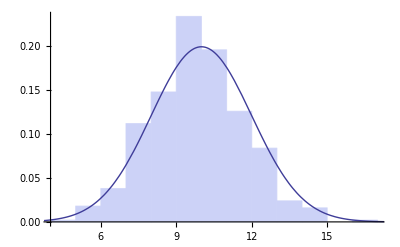

```mathematica
(* 疑似乱数データのヒストグラムに確率密度関数を重ねてみる *)
Module[{g1,g2},
g1=Plot[PDF[NormalDistribution[10,2],x],{x,0,30}];
g2=Histogram[Table[RandomReal[NormalDistribution[10,2]],{500}],Automatic,"Probability"];
Show[g2,g1]
]
```

### 兵士達はランダムマッチングにより一対一で戦う．

```mathematica
(* ここで各国の兵数を一般化する *)
Module[{id1,id2,n1=15,n2=15,power1,power2,winner1,winner2},
power1=Table[RandomReal[NormalDistribution[10,1]],{n1}];
power2=Table[RandomReal[NormalDistribution[11,1]],{n2}];
id1=Range[n1];(*初期兵ID*)
id2=Range[n2];(*初期兵ID*)

id1=RandomSample[Range[n1]];
id2=RandomSample[Range[n2]];(*　ランダムに並び替える　*)
{id1,id2}
]
```

{{7,24,27,22,30,11,16,14,21,23,18,9,4,25,12,26,6,8,1,10,28,5,3,2,20,19,17,29,13,15},{21,18,22,9,26,19,30,11,29,1,16,4,17,15,27,23,13,25,14,6,24,5,3,2,12,8,28,10,7,20}}

```mathematica
Q ランダムマッチングで順序対を作りなさい
```

### 対戦した兵士のうち，武力の高い兵士が勝負に勝ち，次の対戦に進む．

```mathematica
(* ここで各国の兵数を一般化する *)
Module[{id1,id2,n1=30,n2=30,power1,power2,winner1,winner2},
power1=Table[RandomReal[NormalDistribution[10,1]],{n1}];
power2=Table[RandomReal[NormalDistribution[11,1]],{n2}];
id1=Range[n1];(*初期兵ID*)
id2=Range[n2];(*初期兵ID*)

id1=RandomSample[Range[n1]];
id2=RandomSample[Range[n2]];(*　ランダムに並び替える　*)
winner1=Table[
If[power1⟦id1⟦i⟧⟧>power2⟦id2⟦i⟧⟧,id1⟦i⟧,Null],
{i,1,Min[Length[id1],Length[id2]]}];
winner1=Select[winner1,#>0&];Print[{"戦闘後1",winner1}];

winner2=Table[
If[power1⟦id1⟦i⟧⟧<power2⟦id2⟦i⟧⟧,id2⟦i⟧,Null],
{i,1,Min[Length[id1],Length[id2]]}];
winner2=Select[winner2,#>0&];Print[{"戦闘後2",winner2}];
]
```

{戦闘後1,{20,5,23,9,18,21}}

{戦闘後2,{14,12,21,1,6,4,19,10,17,29,8,11,22,18,3,23,26,27,30,13,7,28,20,15}}

## 反復戦闘用コード

### 片方の集団が全滅するまで戦闘を反復するModule

```mathematica
Module[{id1,id2,n1=10,n2=10,power1,power2,winner1,winner2,reserve1,reserve2},

power1=Table[RandomReal[NormalDistribution[10,1]],{n1}];(*初期兵力*)
power2=Table[RandomReal[NormalDistribution[11,1]],{n2}];(*初期兵力*)

id1=Range[n1];(*初期兵ID*)
id2=Range[n2];(*初期兵ID*)

Print[TableForm[{id1,power1}]];(*ID別初期兵力*)
Print[TableForm[{id2,power2}]];

While[(Length[id1]>0)&&(Length[id2]>0),(*戦闘終了条件*)
winner1={};(*戦闘勝者リストの初期化*)
winner2={};

id1=RandomSample[id1];Print[{"G1:出撃する兵士のID",id1}];
id2=RandomSample[id2];Print[{"G2:出撃する兵士のID",id2}];
(*Print[Table[{power1⟦id1⟦i⟧⟧,power2⟦id2⟦i⟧⟧},{i,1,Min[Length[id1],Length[id2]]}]];*)

Table[
If[
power1⟦id1⟦i⟧⟧>power2⟦id2⟦i⟧⟧,
winner1=Append[winner1,id1⟦i⟧],
winner2=Append[winner2,id2⟦i⟧]
](* If *),
{i,1,Min[Length[id1],Length[id2]]}](* Table *);

Print[{"G1:戦闘で勝った兵士",winner1}];
Print[{"G2:戦闘で勝った兵士",winner2}];

reserve1=If[Length[id1]>Length[id2],Table[id1⟦i⟧,{i,Length[id2]+1,Length[id1]}],{}];(* 予備役の招集　*)
reserve2=If[Length[id2]>Length[id1],Table[id2⟦i⟧,{i,Length[id1]+1,Length[id2]}],{}];

id1=Append[winner1,reserve1]//Flatten;
id2=Append[winner2,reserve2]//Flatten;
Print[{"G1:残存兵",id1}];
Print[{"G2:残存兵",id2}]](* while *)
]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
8.89909 | 10.8493 | 8.60179 | 10.0509 | 10.619 | 10.434 | 10.3921 | 9.71153 | 10.2917 | 11.4429

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
10.1767 | 9.05101 | 10.8939 | 10.3497 | 10.7659 | 10.1089 | 9.66295 | 11.9711 | 10.7933 | 11.5292

{G1:出撃する兵士のID,{1,6,2,7,4,3,5,8,10,9}}

{G2:出撃する兵士のID,{1,9,5,8,7,2,3,4,10,6}}

{G1:戦闘で勝った兵士,{2,4,9}}

{G2:戦闘で勝った兵士,{1,9,8,2,3,4,10}}

{G1:残存兵,{2,4,9}}

{G2:残存兵,{1,9,8,2,3,4,10}}

{G1:出撃する兵士のID,{2,9,4}}

{G2:出撃する兵士のID,{1,8,4,10,3,9,2}}

{G1:戦闘で勝った兵士,{2}}

{G2:戦闘で勝った兵士,{8,4}}

{G1:残存兵,{2}}

{G2:残存兵,{8,4,10,3,9,2}}

{G1:出撃する兵士のID,{2}}

{G2:出撃する兵士のID,{3,4,8,2,9,10}}

{G1:戦闘で勝った兵士,{}}

{G2:戦闘で勝った兵士,{3}}

{G1:残存兵,{}}

{G2:残存兵,{3,4,8,2,9,10}}

# 問題集

## 上記アルゴリズムが正しければ，武力の高い兵士（仮に呂布と呼ぶ）はたった一人でも生き残るはずである． 呂布が生き残るかどうか確認せよ

### ヒント

```mathematica
power1⟦n1⟧=100;(* 戦闘力100（呂布）を集団1の最後に追加するコマンド例 *)
```

### 解答例

```mathematica
(*片方の集団が全滅するまで戦闘を反復するModule *)
Module[{id1,id2,n1=50,n2=50,power1,power2,winner1,winner2,reserve1,reserve2},

power1=Table[RandomReal[NormalDistribution[10,1]],{n1}];(*初期兵力*)
power2=Table[RandomReal[NormalDistribution[11,1]],{n2}];(*初期兵力*)
power1⟦n1⟧=100;(* 戦闘力100（呂布）を追加するコマンド例 *)

id1=Range[n1];(*初期兵ID*)
id2=Range[n2];(*初期兵ID*)

Print[TableForm[{id1,power1}]];(*ID別初期兵力*)
Print[TableForm[{id2,power2}]];

While[(Length[id1]>0)&&(Length[id2]>0),(*戦闘終了条件*)
winner1={};(*戦闘勝者リストの初期化*)
winner2={};

id1=RandomSample[id1];Print[{"G1:出撃する兵士のID",id1}];
id2=RandomSample[id2];Print[{"G2:出撃する兵士のID",id2}];
(*Print[Table[{power1⟦id1⟦i⟧⟧,power2⟦id2⟦i⟧⟧},{i,1,Min[Length[id1],Length[id2]]}]];*)

Table[
If[
power1⟦id1⟦i⟧⟧>power2⟦id2⟦i⟧⟧,
winner1=Append[winner1,id1⟦i⟧],
winner2=Append[winner2,id2⟦i⟧]
](* If *),
{i,1,Min[Length[id1],Length[id2]]}](* Table *);

Print[{"G1:戦闘で勝った兵士",winner1}];
Print[{"G2:戦闘で勝った兵士",winner2}];

reserve1=If[Length[id1]>Length[id2],Table[id1⟦i⟧,{i,Length[id2]+1,Length[id1]}],{}];(* 予備役の招集　*)
reserve2=If[Length[id2]>Length[id1],Table[id2⟦i⟧,{i,Length[id1]+1,Length[id2]}],{}];

id1=Append[winner1,reserve1]//Flatten;
id2=Append[winner2,reserve2]//Flatten;
](* while 終了*)
]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50
9.05589 | 10.6014 | 9.77316 | 8.48265 | 9.47502 | 8.78762 | 9.28114 | 11.2145 | 11.62 | 10.0551 | 10.2889 | 10.9877 | 10.706 | 10.0003 | 9.82949 | 9.26945 | 8.78237 | 11.3027 | 9.45999 | 9.50657 | 11.5565 | 7.65151 | 9.38067 | 10.1689 | 9.1065 | 12.2302 | 9.29772 | 8.64932 | 10.1506 | 8.87674 | 9.76609 | 10.4045 | 12.2698 | 10.6854 | 11.7766 | 10.8117 | 9.67724 | 10.7426 | 9.51958 | 7.99594 | 10.875 | 11.302 | 9.49843 | 8.39175 | 8.86488 | 9.61272 | 12.0064 | 10.674 | 9.52438 | 100

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20 | 21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30 | 31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40 | 41 | 42 | 43 | 44 | 45 | 46 | 47 | 48 | 49 | 50
11.0251 | 11.3089 | 12.4071 | 11.5165 | 10.1506 | 11.1631 | 12.3411 | 11.0683 | 10.7743 | 10.6351 | 11.3093 | 10.9238 | 10.6627 | 11.8872 | 10.2949 | 10.0946 | 8.97668 | 9.06611 | 11.0772 | 9.59052 | 9.26735 | 12.1289 | 11.7958 | 10.2533 | 12.8649 | 10.8892 | 11.6431 | 11.4448 | 12.3571 | 9.99593 | 10.5051 | 11.9851 | 11.6768 | 10.8348 | 11.0462 | 10.4154 | 12.5786 | 9.05254 | 10.0728 | 9.98291 | 11.6037 | 10.237 | 12.1452 | 12.259 | 11.7849 | 10.1357 | 11.3367 | 10.7634 | 12.6902 | 11.9667

{G1:出撃する兵士のID,{41,37,43,25,15,26,4,6,50,49,33,40,36,2,46,44,17,1,16,42,48,19,32,45,39,20,28,7,5,24,13,3,11,31,8,34,23,27,10,47,38,29,21,35,30,12,22,9,14,18}}

{G2:出撃する兵士のID,{11,25,29,4,20,42,18,27,49,8,44,2,32,46,12,13,43,28,50,6,34,35,5,47,31,17,40,10,7,22,16,3,39,45,19,37,23,48,15,38,26,14,41,9,30,24,33,21,1,36}}

{G1:戦闘で勝った兵士,{15,26,50,33,2,42,32,20,13,11,8,47,35,12,9,18}}

{G2:戦闘で勝った兵士,{11,25,29,4,18,27,8,2,32,12,13,43,28,50,34,35,47,31,40,10,7,22,3,45,37,23,48,15,26,14,41,30,33,1}}

{G1:出撃する兵士のID,{9,8,20,26,11,42,35,12,13,18,50,15,47,33,2,32}}

{G2:出撃する兵士のID,{43,1,12,26,15,32,37,14,35,13,4,45,10,3,22,7,30,31,27,48,50,23,18,2,25,40,33,34,47,41,28,11,29,8}}

{G1:戦闘で勝った兵士,{8,26,18,50,47}}

{G2:戦闘で勝った兵士,{43,12,15,32,37,14,35,45,3,22,7}}

{G1:出撃する兵士のID,{26,50,47,8,18}}

{G2:出撃する兵士のID,{32,11,41,48,29,35,27,8,43,3,22,50,30,2,25,12,7,28,34,47,37,23,15,18,31,40,45,14,33}}

{G1:戦闘で勝った兵士,{26,50,47,8}}

{G2:戦闘で勝った兵士,{29}}

{G1:出撃する兵士のID,{50,8,26,47}}

{G2:出撃する兵士のID,{29,35,3,7,8,14,33,47,18,12,27,23,50,25,2,30,40,37,34,31,43,22,15,28,45}}

{G1:戦闘で勝った兵士,{50,8}}

{G2:戦闘で勝った兵士,{3,7}}

{G1:出撃する兵士のID,{8,50}}

{G2:出撃する兵士のID,{12,7,40,47,50,31,2,33,30,45,8,25,23,37,15,27,34,28,3,14,22,18,43}}

{G1:戦闘で勝った兵士,{8,50}}

{G2:戦闘で勝った兵士,{}}

{G1:出撃する兵士のID,{50,8}}

{G2:出撃する兵士のID,{40,25,50,43,28,47,27,45,23,18,37,2,3,22,14,30,34,31,15,33,8}}

{G1:戦闘で勝った兵士,{50}}

{G2:戦闘で勝った兵士,{25}}

{G1:出撃する兵士のID,{50}}

{G2:出撃する兵士のID,{28,27,15,2,8,33,34,43,37,45,22,30,14,50,31,3,25,23,18,47}}

{G1:戦闘で勝った兵士,{50}}

{G2:戦闘で勝った兵士,{}}

{G1:出撃する兵士のID,{50}}

{G2:出撃する兵士のID,{47,15,33,34,43,18,31,50,30,25,14,3,8,27,37,2,23,45,22}}

{G1:戦闘で勝った兵士,{50}}

{G2:戦闘で勝った兵士,{}}

{G1:出撃する兵士のID,{50}}

{G2:出撃する兵士のID,{37,43,50,22,27,31,30,25,15,34,18,2,33,3,23,8,45,14}}

{G1:戦闘で勝った兵士,{50}}

{G2:戦闘で勝った兵士,{}}

{G1:出撃する兵士のID,{50}}

{G2:出撃する兵士のID,{33,22,45,31,15,8,27,18,34,23,30,25,50,2,14,3,43}}

{G1:戦闘で勝った兵士,{50}}

{G2:戦闘で勝った兵士,{}}

{G1:出撃する兵士のID,{50}}

{G2:出撃する兵士のID,{45,30,25,3,27,15,34,14,43,23,31,22,18,50,2,8}}

{G1:戦闘で勝った兵士,{50}}

{G2:戦闘で勝った兵士,{}}

{G1:出撃する兵士のID,{50}}

{G2:出撃する兵士のID,{18,50,30,43,25,2,14,15,23,3,31,27,34,22,8}}

{G1:戦闘で勝った兵士,{50}}

{G2:戦闘で勝った兵士,{}}

{G1:出撃する兵士のID,{50}}

{G2:出撃する兵士のID,{14,27,22,8,30,2,3,43,50,34,25,15,31,23}}

{G1:戦闘で勝った兵士,{50}}

{G2:戦闘で勝った兵士,{}}

{G1:出撃する兵士のID,{50}}

{G2:出撃する兵士のID,{50,30,34,3,8,23,43,22,2,31,25,15,27}}

{G1:戦闘で勝った兵士,{50}}

{G2:戦闘で勝った兵士,{}}

{G1:出撃する兵士のID,{50}}

{G2:出撃する兵士のID,{15,31,3,2,27,43,8,30,25,34,23,22}}

{G1:戦闘で勝った兵士,{50}}

{G2:戦闘で勝った兵士,{}}

{G1:出撃する兵士のID,{50}}

{G2:出撃する兵士のID,{8,34,43,27,23,2,30,22,3,31,25}}

{G1:戦闘で勝った兵士,{50}}

{G2:戦闘で勝った兵士,{}}

{G1:出撃する兵士のID,{50}}

{G2:出撃する兵士のID,{2,23,30,25,22,43,27,3,34,31}}

{G1:戦闘で勝った兵士,{50}}

{G2:戦闘で勝った兵士,{}}

{G1:出撃する兵士のID,{50}}

{G2:出撃する兵士のID,{34,25,43,22,31,30,27,3,23}}

{G1:戦闘で勝った兵士,{50}}

{G2:戦闘で勝った兵士,{}}

{G1:出撃する兵士のID,{50}}

{G2:出撃する兵士のID,{22,3,43,30,31,23,25,27}}

{G1:戦闘で勝った兵士,{50}}

{G2:戦闘で勝った兵士,{}}

{G1:出撃する兵士のID,{50}}

{G2:出撃する兵士のID,{25,27,30,43,31,3,23}}

{G1:戦闘で勝った兵士,{50}}

{G2:戦闘で勝った兵士,{}}

{G1:出撃する兵士のID,{50}}

{G2:出撃する兵士のID,{23,3,27,30,31,43}}

{G1:戦闘で勝った兵士,{50}}

{G2:戦闘で勝った兵士,{}}

{G1:出撃する兵士のID,{50}}

{G2:出撃する兵士のID,{30,3,27,31,43}}

{G1:戦闘で勝った兵士,{50}}

{G2:戦闘で勝った兵士,{}}

{G1:出撃する兵士のID,{50}}

{G2:出撃する兵士のID,{31,43,3,27}}

{G1:戦闘で勝った兵士,{50}}

{G2:戦闘で勝った兵士,{}}

{G1:出撃する兵士のID,{50}}

{G2:出撃する兵士のID,{43,27,3}}

{G1:戦闘で勝った兵士,{50}}

{G2:戦闘で勝った兵士,{}}

{G1:出撃する兵士のID,{50}}

{G2:出撃する兵士のID,{3,27}}

{G1:戦闘で勝った兵士,{50}}

{G2:戦闘で勝った兵士,{}}

{G1:出撃する兵士のID,{50}}

{G2:出撃する兵士のID,{27}}

{G1:戦闘で勝った兵士,{50}}

{G2:戦闘で勝った兵士,{}}

## 少数の精鋭は, 大軍団に対抗できるかどうか確認せよ

### 解答例1

```mathematica
勝敗は決定論的ではなく，確率論的であると仮定する
```

### 片方の集団が全滅するまで戦闘を反復するModule

```mathematica
battlesim[n1_,n2_,m1_,s1_,m2_,s2_]:=Module[{id1,id2,power1,power2,winner1,winner2,reserve1,reserve2},

power1=Table[RandomReal[NormalDistribution[m1,s1]],{n1}];(*初期兵力*)
power2=Table[RandomReal[NormalDistribution[m2,s2]],{n2}];(*初期兵力*)
id1=Range[n1];id2=Range[n2];(*初期兵ID*)

While[(Length[id1]>0)&&(Length[id2]>0),(*戦闘終了条件*)
winner1={};(*戦闘勝者リストの初期化*)
winner2={};

id1=RandomSample[id1];Print[{"G1:出撃する兵士のID",id1}];
id2=RandomSample[id2];Print[{"G2:出撃する兵士のID",id2}];
(*Print[Table[{power1⟦id1⟦i⟧⟧,power2⟦id2⟦i⟧⟧},{i,1,Min[Length[id1],Length[id2]]}]];*)

Table[
If[
power1⟦id1⟦i⟧⟧>power2⟦id2⟦i⟧⟧,
winner1=Append[winner1,id1⟦i⟧],
winner2=Append[winner2,id2⟦i⟧]
](* If *),
{i,1,Min[Length[id1],Length[id2]]}](* Table *);

Print[{"G1:戦闘で勝った兵士",winner1}];
Print[{"G2:戦闘で勝った兵士",winner2}];

reserve1=If[Length[id1]>Length[id2],Table[id1⟦i⟧,{i,Length[id2]+1,Length[id1]}],{}];(* 予備役の招集　*)
reserve2=If[Length[id2]>Length[id1],Table[id2⟦i⟧,{i,Length[id1]+1,Length[id2]}],{}];

id1=Append[winner1,reserve1]//Flatten;
id2=Append[winner2,reserve2]//Flatten;
Print[{"G1:残存兵",id1}];
Print[{"G2:残存兵",id2}]](* while *)
]
```

```mathematica
battlesim[10,15,50,5,45,5]
```

{G1:出撃する兵士のID,{9,7,10,6,4,1,2,3,8,5}}

{G2:出撃する兵士のID,{7,6,9,8,12,1,3,5,15,2,14,13,4,10,11}}

{G1:戦闘で勝った兵士,{9,7,10,6,4,1,3,5}}

{G2:戦闘で勝った兵士,{3,15}}

{G1:残存兵,{9,7,10,6,4,1,3,5}}

{G2:残存兵,{3,15,14,13,4,10,11}}

{G1:出撃する兵士のID,{3,6,10,4,9,5,7,1}}

{G2:出撃する兵士のID,{4,3,15,13,14,10,11}}

{G1:戦闘で勝った兵士,{3,6,4,9,7}}

{G2:戦闘で勝った兵士,{15,10}}

{G1:残存兵,{3,6,4,9,7,1}}

{G2:残存兵,{15,10}}

{G1:出撃する兵士のID,{6,1,3,4,9,7}}

{G2:出撃する兵士のID,{10,15}}

{G1:戦闘で勝った兵士,{6}}

{G2:戦闘で勝った兵士,{15}}

{G1:残存兵,{6,3,4,9,7}}

{G2:残存兵,{15}}

{G1:出撃する兵士のID,{6,4,7,9,3}}

{G2:出撃する兵士のID,{15}}

{G1:戦闘で勝った兵士,{6}}

{G2:戦闘で勝った兵士,{}}

{G1:残存兵,{6,4,7,9,3}}

{G2:残存兵,{}}

## 兵士のモラルが戦闘力に影響する状況を表現して，一人の豪傑が不利な戦局を覆すということがありえるかどうか分析せよ

## このプログラムを修正して同時に複数人が戦う状況 （部隊戦闘） を表現せよ

## このプログラムのグラフィカルな出力を考案し，Manipulateで動的なプレゼンテーションを作れ

### 作成例1

```mathematica
手順
一回の戦闘毎の人数だけを出力するようにoutputを調整して，関数化する
1.Doのまえにikinokori={{na,nb}}(*戦闘前の人数をカウント*)を定義
2.Do内部の最後にikinokori=Append[ikinokori,{Length[id1],Length[id2]}]を追加
3.Do終了後にikinokoriを出力．
4.パラメータを関数化
5.関数をManipulateで視覚化する
```

```mathematica
battle[time_,na_,nb_,ma_,sa_,mb_,sb_]:=Module[{id1,id2,A,B,Apower,Bpower,Awinner,Bwinner,reserve1,reserve2,ikinokori},
Apower=Table[RandomReal[NormalDistribution[ma,sa]],{na}];
Bpower=Table[RandomReal[NormalDistribution[mb,sb]],{nb}];
id1=Range[na];(*初期兵ID*)
id2=Range[nb];(*初期兵ID*)
ikinokori={{na,nb}};(*戦闘前の人数をカウント*)

Do[
id1=RandomSample[id1];(*Print[{初期兵ID対戦順,id1}];*)
id2=RandomSample[id2];(*Print[{初期兵ID対戦順,id2}];*)
(*Print[Table[{Apower⟦id1⟦i⟧⟧,Bpower⟦id2⟦i⟧⟧},{i,1,Min[Length[id1],Length[id2]]}]];*)

(*Aの戦闘者の生き残りID*)
Awinner=Table[
If[Apower⟦id1⟦i⟧⟧>Bpower⟦id2⟦i⟧⟧,id1⟦i⟧,Null],
{i,1,Min[Length[id1],Length[id2]]}];
Awinner=Select[Awinner,#>0&];(*Print[{A戦闘後,Awinner}];*)

Bwinner=Table[
If[Apower⟦id1⟦i⟧⟧<Bpower⟦id2⟦i⟧⟧,id2⟦i⟧,Null],
{i,1,Min[Length[id1],Length[id2]]}];
Bwinner=Select[Bwinner,#>0&];(*Print[{B戦闘後,Bwinner}];*)

reserve1=If[Length[id1]>Length[id2],Table[id1⟦i⟧,{i,Length[id2]+1,Length[id1]}],{}];(* 予備役の招集　*)
reserve2=If[Length[id2]>Length[id1],Table[id2⟦i⟧,{i,Length[id1]+1,Length[id2]}],{}];

id1=Append[Awinner,reserve1]//Flatten;
id2=Append[Bwinner,reserve2]//Flatten;
(*Print[{リザーブアーミー追加後,id1}];Print[{リザーブアーミー追加後,id2}]*)
ikinokori=Append[ikinokori,{Length[id1],Length[id2]}]
,{time}];
Transpose[ikinokori]
]
```

```mathematica
battle[10,50,50,10,1,11,1]
```

{{50,11,3,3,1,1,1,0,0,0,0},{50,39,36,33,32,31,30,30,30,30,30}}

```mathematica
Manipulate[ListPlot[battle[time,na,nb,ma,sa,mb,sb],Filling->Axis,
PlotStyle->{{Red,PointSize[Large]},{Blue,PointSize[Large]}}],
{{time,5},1,20},
{{na,30,"A兵士数"},20,100},
{{nb,30,"B兵士数"},20,100},
{{ma,10,"A平均"},1,30},{{sa,1,"A標準偏差"},0.5,5},
{{mb,11,"B平均"},1,30},{{sb,1,"B標準偏差"},0.5,5},ControlPlacement->Left]
```

ListPlot::lpn: battle[14.187,30.,30.,10.,1.,11.,1.]は数値のリストあるいは数値の対のリストではありません．

General::stop: この計算中に，ListPlot::lpnのこれ以上の出力は表示されません．

```mathematica
Dynamic[]　や　Refresh[]　を利用してリアルタイムに分布を表示してみよう
```